```mathematica
ClearAll["Global`*"]
```

```mathematica
xl=0;
xr=1;
```

```mathematica
(*test case 1*)
```

```mathematica
z[x_]:=x^4/48
```

```mathematica
z'[x]
```

x^3/12

```mathematica
D[z[x]z'[x],x]
```

(7 x^6)/576

```mathematica
D[D[z[x]z'[x],x],x]
```

(7 x^5)/96

```mathematica
D[D[D[z[x]z'[x],x],x],x]
```

(35 x^4)/96

```mathematica
(*check for z*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fourth_order_pde/solution/z.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

```mathematica
δ=Max[Table[Abs[t[[i,2]]-u[t[[i,1]]]],{i,1,Length[t]}]]
```

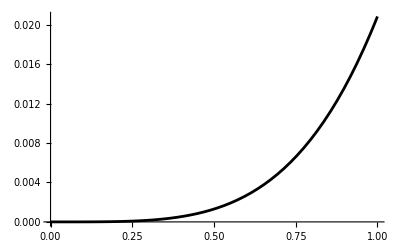

```mathematica
plotzexact=Plot[z[x],{x,xl,xr},PlotRange->Full,PlotStyle->Black]
```

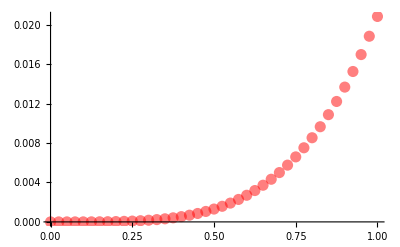

```mathematica
plotznum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[0.5],PointSize->0.02}]
```

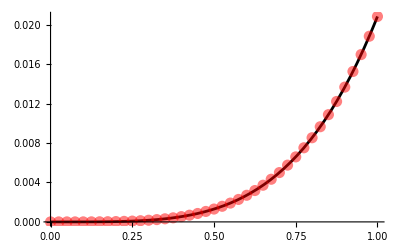

```mathematica
Show[plotzexact,plotznum]
```